## Sigmoidal Dielectric Profile

### Sigmoidal function

```mathematica
c[z_]:=1/(1+Exp[-z])
```

### Dielectric Profile

```mathematica
ϵSubs=ϵ->ϵL((ϵR-ϵL)/ϵL c[z/M]+c[L/M]-((ϵR-ϵL)/ϵL+1)c[-L/M])/(c[L/M]-c[-L/M])
```

ϵ→(ϵL (1/(1+ⅇ^(-L/M))+(-ϵL+ϵR)/((1+ⅇ^(-z/M)) ϵL)-(1+(-ϵL+ϵR)/ϵL)/(1+ⅇ^(L/M))))/(1/(1+ⅇ^(-L/M))-1/(1+ⅇ^(L/M)))

```mathematica
ϵ/.ϵSubs/.{ϵL->Subscript[ϵ, L],ϵR->Subscript[ϵ, R]}//Simplify
```

((ⅇ^(L/M)-ⅇ^(z/M)) ϵ_L+(-1+ⅇ^((L+z)/M)) ϵ_R)/((-1+ⅇ^(L/M)) (1+ⅇ^(z/M)))

### Simplified general expression

```mathematica
A=(ϵR cc[-L/M]-ϵL cc[L/M]+(ϵL-ϵR) cc[z/M])/(cc[-L/M]-cc[L/M])
```

## ODE Construction

### Dimensional Formulation

```mathematica
odeXz=Ex''[z]+ϵ μ ω^2 Ex[z]==0
```

ϵ μ ω^2 Ex[z]+Ex''[z]==0

### Dimension - Free Grouping

```mathematica
qSubs=q->r c[s]+c[a]-(r+1)c[-a]
```

q→1/(1+ⅇ^-a)+r/(1+ⅇ^-s)-(1+r)/(1+ⅇ^a)

```mathematica
odeXsDG=(Ex''[s]+(q Ω^2)/(c[a]-c[-a])Ex[s]==0)/.qSubs
```

((1/(1+ⅇ^-a)+r/(1+ⅇ^-s)-(1+r)/(1+ⅇ^a)) Ω^2 Ex[s])/(1/(1+ⅇ^-a)-1/(1+ⅇ^a))+Ex''[s]==0

## Small effective dielectric dynamic range

```mathematica
QrSmall=Normal[Series[Coefficient[odeXsDG[[1]],Ex[s]],{r,0,1}]]
```

Ω^2+((-1+ⅇ^(a+s)) r Ω^2)/((-1+ⅇ^a) (1+ⅇ^s))

### Regular Perturbation : r<<((-1+ⅇ^(a+s)) Ω^2)/((-1+ⅇ^a) (1+ⅇ^s)): Not trackable

```mathematica
rRegularPerSubs = {Ex[s]->Ex0[s]+r Ex1[s],Ex''[s]->Ex0''[s]+r Ex1''[s]}
```

{Ex[s]→Ex0[s]+r Ex1[s],Ex''[s]→Ex0''[s]+r Ex1''[s]}

```mathematica
odeXsColr=Collect[Apart[odeXsDG[[1]]/.rRegularPerSubs],r,Simplify]
```

Ω^2 Ex0[s]+((-1+ⅇ^(a+s)) r^2 Ω^2 Ex1[s])/((-1+ⅇ^a) (1+ⅇ^s))+Ex0''[s]+(r ((-1+ⅇ^(a+s)) Ω^2 Ex0[s]+(-1+ⅇ^a) (1+ⅇ^s) (Ω^2 Ex1[s]+Ex1''[s])))/((-1+ⅇ^a) (1+ⅇ^s))

```mathematica
odeXsColr0=Coefficient[odeXsColr,r,0]
```

Ω^2 Ex0[s]+Ex0''[s]

```mathematica
odeXsColr1=Collect[Coefficient[odeXsColr,r,1],{Ex0[s],Ex1''[s],Ex1[s]}]
```

((-1+ⅇ^(a+s)) Ω^2 Ex0[s])/((-1+ⅇ^a) (1+ⅇ^s))+Ω^2 Ex1[s]+Ex1''[s]

```mathematica
DSolve[odeXsColr0==0,Ex0[s],s]
```

{{Ex0[s]→C[1] Cos[s Ω]+C[2] Sin[s Ω]}}

```mathematica
DSolve[(odeXsColr1==0)/.Ex0[s]->Exp[-Ω s],Ex1,s]//Simplify
```

{{Ex1→Function[{s},C[1] Cos[s Ω]+C[2] Sin[s Ω]+1/(-1+ⅇ^a)(1/4+ⅈ/4) ⅇ^((-1-ⅈ) s Ω) (-ⅇ^a Cos[s Ω]+ⅈ ⅇ^(a+2 ⅈ s Ω) Cos[s Ω]+Cos[s Ω] Hypergeometric2F1[1,(-1-ⅈ) Ω,1-(1+ⅈ) Ω,-ⅇ^s]+ⅇ^a Cos[s Ω] Hypergeometric2F1[1,(-1-ⅈ) Ω,1-(1+ⅈ) Ω,-ⅇ^s]-ⅈ ⅇ^(2 ⅈ s Ω) Cos[s Ω] Hypergeometric2F1[1,(-1+ⅈ) Ω,1-(1-ⅈ) Ω,-ⅇ^s]-ⅈ ⅇ^(a+2 ⅈ s Ω) Cos[s Ω] Hypergeometric2F1[1,(-1+ⅈ) Ω,1-(1-ⅈ) Ω,-ⅇ^s]-ⅈ ⅇ^a Sin[s Ω]+ⅇ^(a+2 ⅈ s Ω) Sin[s Ω]+ⅈ Hypergeometric2F1[1,(-1-ⅈ) Ω,1-(1+ⅈ) Ω,-ⅇ^s] Sin[s Ω]+ⅈ ⅇ^a Hypergeometric2F1[1,(-1-ⅈ) Ω,1-(1+ⅈ) Ω,-ⅇ^s] Sin[s Ω]-ⅇ^(2 ⅈ s Ω) Hypergeometric2F1[1,(-1+ⅈ) Ω,1-(1-ⅈ) Ω,-ⅇ^s] Sin[s Ω]-ⅇ^(a+2 ⅈ s Ω) Hypergeometric2F1[1,(-1+ⅈ) Ω,1-(1-ⅈ) Ω,-ⅇ^s] Sin[s Ω])]}}

## Large effective dielectric dynamic range

```mathematica
Collect[Coefficient[odeXsDG[[1]],Ex[s]],r,Simplify]
```

Ω^2+((-1+ⅇ^(a+s)) r Ω^2)/((-1+ⅇ^a) (1+ⅇ^s))

## Thin layer: |s|<a<<1

```mathematica
QaSmall=Collect[Normal[Series[Coefficient[odeXsDG[[1]]/Ω^2,Ex[s]],{a,0,1},{s,0,1}]],r]
```

1+r (1/2+s/(2 a)+(a s)/24)

#### The term (a s)/24 neglected - O(a^2)

```mathematica
odeQaSmall=Ex''[s]+Ω^2(1+r (1/2+s/(2 a))) Ex[s]==0
```

(1+r (1/2+s/(2 a))) Ω^2 Ex[s]+Ex''[s]==0

### Regular Perturbation r<< (1/2+s/(2 a))~1

```mathematica
odeQaSmallColr=Collect[odeQaSmall[[1]]/.rRegularPerSubs,r,Simplify]
```

Ω^2 Ex0[s]+(r^2 (a+s) Ω^2 Ex1[s])/(2 a)+Ex0''[s]+r (((a+s) Ω^2 Ex0[s])/(2 a)+Ω^2 Ex1[s]+Ex1''[s])

```mathematica
odeQaSmallColr0=Coefficient[odeQaSmallColr,r,0]
```

Ω^2 Ex0[s]+Ex0''[s]

```mathematica
odeQaSmallColr1=Coefficient[odeQaSmallColr,r,1]
```

((a+s) Ω^2 Ex0[s])/(2 a)+Ω^2 Ex1[s]+Ex1''[s]

```mathematica
Collect[TrigToExp[DSolve[0==odeQaSmallColr1/.Ex0[s]->B Exp[I Ω s],Ex1[s],s]],{Exp[-I s Ω],Exp[I s Ω]},Simplify]
```

{{Ex1[s]→(ⅇ^(ⅈ s Ω) (ⅈ B (-1+2 ⅈ s Ω+2 s^2 Ω^2+2 a Ω (ⅈ+2 s Ω))+8 a Ω (C[1]-ⅈ C[2])))/(16 a Ω)+1/2 ⅇ^(-ⅈ s Ω) (C[1]+ⅈ C[2])}}

### WKB

```mathematica
ThinLayerPhase=Integrate[√(1+r(1/2+s/(2a))),s]//Simplify
```

(√2 (a (2+r)+r s) √(2+r+(r s)/a))/(3 r)

```mathematica
Series[ThinLayerPhase,{a,0,2}]
```

(√2 s √(r s))/(3 √a)+((2+r) √(r s) √a)/(√2 r)+((2+r)^2 √(r s) a^(3/2))/(4 √2 r^2 s)+O[a]^(5/2)

```mathematica
Series[ThinLayerPhase,{r,0,2}]
```

(4 a)/(3 r)+(a+s)+((a+s)^2 r)/(8 a)-((a+s)^3 r^2)/(96 a^2)+O[r]^3

```mathematica
PhysicalOpticsThinLayer=(1+r(1/2+s/(2a)))^(-1/4)Exp[I Ω ThinLayerPhase]
```

ⅇ^((ⅈ √2 (a (2+r)+r s) √(2+r+(r s)/a) Ω)/(3 r))/(1+r (1/2+s/(2 a)))^(1/4)

```mathematica
D[PhysicalOpticsThinLayer,s]//Simplify
```

(ⅈ ⅇ^((ⅈ √2 (a (2+r)+r s) √(2+r+(r s)/a) Ω)/(3 r)) (4 √2 a √(2+r+(r s)/a) Ω+r (ⅈ+2 √2 a √(2+r+(r s)/a) Ω+2 √2 s √(2+r+(r s)/a) Ω)))/(2 2^(3/4) (a (2+r)+r s) (2+r+(r s)/a)^(1/4))

## Thick Layer

```mathematica
QaLarge=Limit[Coefficient[odeXsDG[[1]]/Ω^2,Ex[s]],a->Infinity]
```

(1+ⅇ^s (1+r))/(1+ⅇ^s)

```mathematica
Manipulate[Plot[(1+ⅇ^s (1+r))/(1+ⅇ^s),{s,-8,8}],{r,-10,10}]
```

```mathematica
Collect[Apart[QaLarge],r]
```

1+(1-1/(1+ⅇ^s)) r

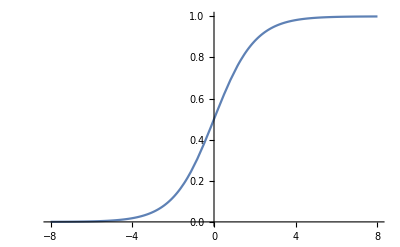

```mathematica
Plot[1-1/(1+ⅇ^s),{s,-8,8}]
```

```mathematica
ThickLayerPhase=Integrate[√QaLarge,s]
```

(√(1+ⅇ^s) √((1+ⅇ^s (1+r))/(1+ⅇ^s)) (s-Log[2+ⅇ^s (2+r)+2 √(1+ⅇ^s) √(1+ⅇ^s (1+r))]+√(1+r) Log[2+r+2 ⅇ^s (1+r)+2 √(1+ⅇ^s) √(1+r) √(1+ⅇ^s (1+r))]))/(√(1+ⅇ^s (1+r)))

```mathematica
Series[ThickLayerPhase,{r,0,1}]
```

s+1/2 (1+Log[4+4 ⅇ^s]) r+O[r]^2

```mathematica
ThickLayerPhaseLargeJumpSer=Series[ThickLayerPhase/.r->1/R,{R,0,0}]//Simplify
```

(Log[1+2 ⅇ^s+2 √(ⅇ^s) √(1+ⅇ^s)]-Log[R])/(√R)+(s-Log[ⅇ^s]+Log[R])+√O[R]

```mathematica
CoefficientList[ThickLayerPhaseLargeJumpSer,R]
```

{s-Log[ⅇ^s]+Log[1+2 ⅇ^s+2 √(ⅇ^s) √(1+ⅇ^s)]/(√R)+Log[R]-Log[R]/(√R)}

```mathematica
Assuming[{Element[s, Reals]},Simplify[ThickLayerPhaseLargeJumpSer/.R->1/r]]
```

(Log[1+2 ⅇ^s+2 √(ⅇ^s (1+ⅇ^s))]-Log[1/r])/(√(1/r))+Log[1/r]+√O[1/r]

## WKB Error Bound

Exp[1/δ S_0+S_1]<<Exp[δ S_2]=1+O(δ S_2)

1/Ω S_2<<1???

```mathematica
S2Func[Q_]:=D[Q,s,s]/(8 Q^(3/2))-5 D[Q,s]^2/(32 Q^(5/2))
```

### Thin Layer :

```mathematica
RelErrThin=1/Ω S2Func[1+r(1/2+s/(2 a))]/.s->a
```

-(5 r^2)/(128 a^2 (1+r)^(5/2) Ω)

### Thick Layer :

```mathematica
RelErrThick=1/Ω S2Func[QaLarge]//Simplify
```

-(ⅇ^s r ((1+ⅇ^s (1+r))/(1+ⅇ^s))^(3/2) (-4+ⅇ^s r+4 ⅇ^(2 s) (1+r)))/(32 (1+ⅇ^s (1+r))^4 Ω)

```mathematica
RelErrThick/.{Exp[s]->1/x,Exp[2s]->1/x^2}//Simplify
```

(r x ((1+r+x)/(1+x))^(3/2) (-r (4+x)+4 (-1+x^2)))/(32 (1+r+x)^4 Ω)

```mathematica
Series[%,{x,0,2}]
```

-(r x)/(8 ((1+r)^(3/2) Ω))+((16 r+5 r^2) x^2)/(32 (1+r)^(5/2) Ω)+O[x]^3

```mathematica
Limit[RelErrThick,s->-Infinity]
```

0